```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}];
(*fileName = "~/Downloads/optimizerHistory.json";*)
```

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

```mathematica
runningBest = FoldList[Max,First[#],Rest[#]]&[raw[[All,"maximizeMe"]]];
```

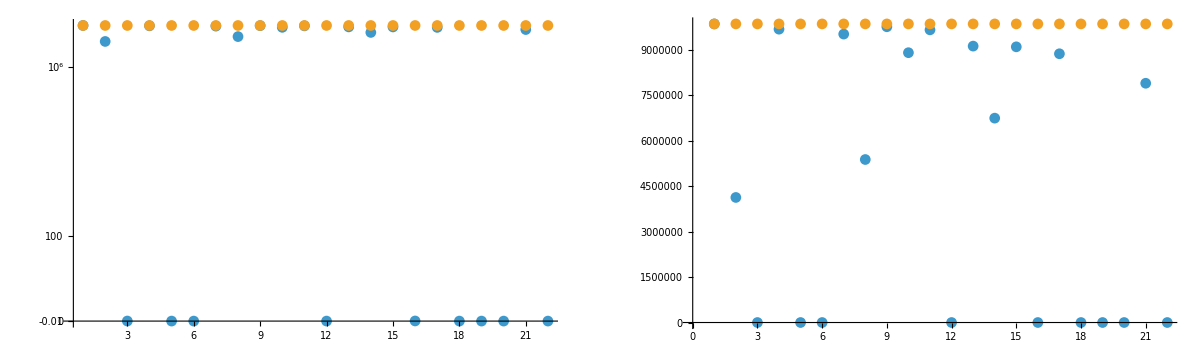

```mathematica
GraphicsGrid[{{
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -19.7576962458
L2PhaseSet : -37.2863812552
L1EnergyOffset : 140726.527142769
L2EnergyOffset : 579322.755693826
L3EnergyOffset : 1.46767090794855773e8
S1ELkG : 773.3623502732
S2ELkG : -2164.5055645385
S3ELkG : -1116.6508888652
S1EL_xOffset : 0.000142492
S1EL_yOffset : -8.8762e-6
S2EL_xOffset : 0.0002620513
S2EL_yOffset : 1.1634e-6
S2ER_xOffset : -0.0000969425
S2ER_yOffset : 0.000015112
S1ER_xOffset : 0.0000149544
S1ER_yOffset : 0.0000170405
XC1FFkG : -0.0065346085
XC3FFkG : 0.0004291352
YC1FFkG : -0.0004258136
YC2FFkG : 0.0012508743
PDrive_median_x : -0.0000168661
PDrive_median_y : -2.5027e-6
PDrive_median_xp : 0.0001548564
PDrive_median_yp : 4.0706e-6
PDrive_median_energy : 9.983211074784404755e9
PDrive_sigmaSI90_x : 0.0000503029
PDrive_sigmaSI90_y : 6.9898e-6
PDrive_sigmaSI90_z : 0.0000487163
PDrive_fitSigma_x : 0.0000141186
PDrive_fitSigma_y : 5.0002e-6
PDrive_fitSigma_z : 7.0649e-6
PDrive_sigmaSI90_xp : 0.000116811
PDrive_sigmaSI90_yp : 0.0000265627
PDrive_sigmaSI90_energy : 9.1367068196557105e7
PDrive_emitSI90_x : 0.0000693999
PDrive_emitSI90_y : 3.6067e-6
PDrive_norm_emit_x : 0.0000388214
PDrive_norm_emit_y : 2.0549e-6
PDrive_charge_nC : 1.599552
PDrive_BMAG_x : 1.7025403062
PDrive_BMAG_y : 1.197047185
PDrive_sliced_BMAG_x : List(3.20014166,5.4321048248,6.1819514007,4.4659785658,1.7196405108)
PDrive_sliced_BMAG_y : List(2.2131669002,1.5545352307,1.1297468232,1.156029808,1.2427219095)
lostChargeFraction : 0.00028
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 9.142e-7
maximizeMe : 9.84500665718489e6
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : True

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{L1PhaseSet,L2PhaseSet,L1EnergyOffset,L2EnergyOffset,L3EnergyOffset,S1ELkG,S2ELkG,S3ELkG,S1EL_xOffset,S1EL_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S1ER_xOffset,S1ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

## Plot specific

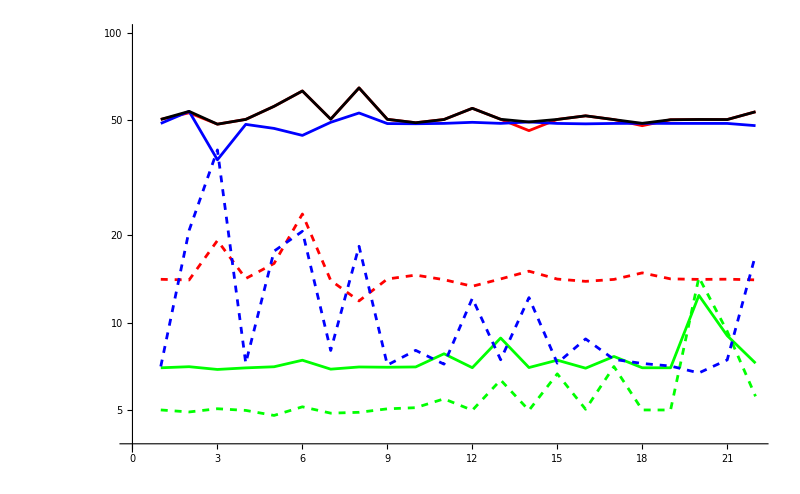

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PDrive_fitSigma_x","PDrive_fitSigma_y","PDrive_fitSigma_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

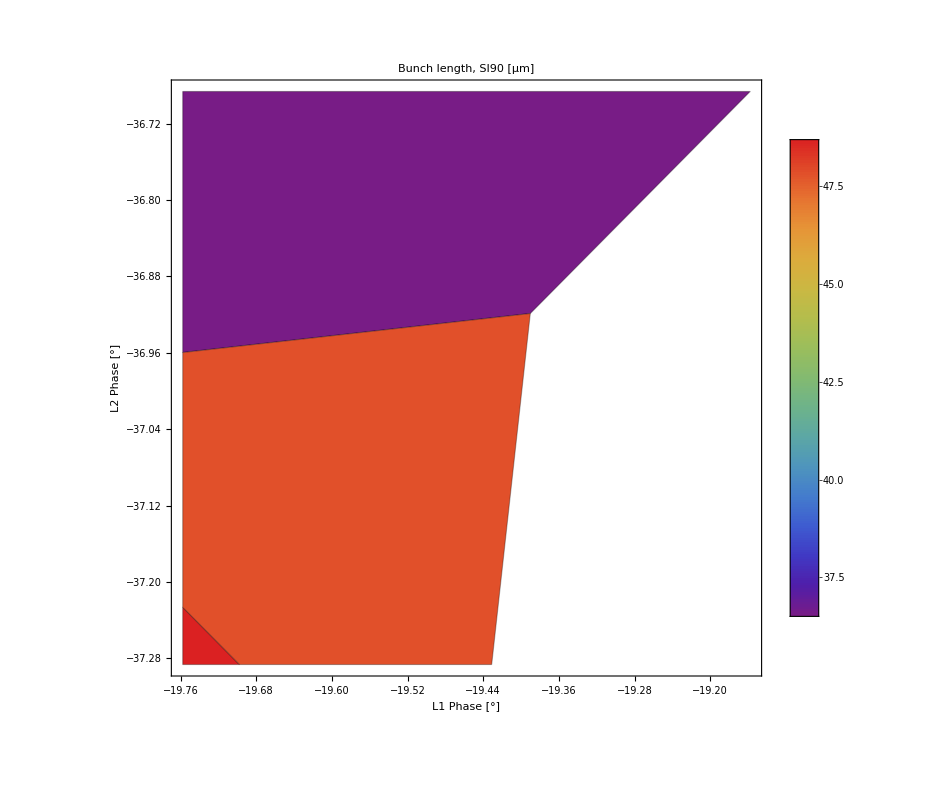

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,
PlotRange->{All,50},
(*PlotRange->{{-35,-21},{-50,-30},{All,50}},*)
Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"]&&MemberQ[Keys[raw[[1]]],"PWitness_sigmaSI90_z"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
]
```

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
#["maximizeMe"]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",
InterpolationOrder->0,
(*PlotRange->{1*^5,All},*)
PlotRange->{{-35,-21},{-50,-30},{1*^5,All}},
Mesh->All,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"maximizeMe",LabelStyle->20]
]
```

-Graphics-

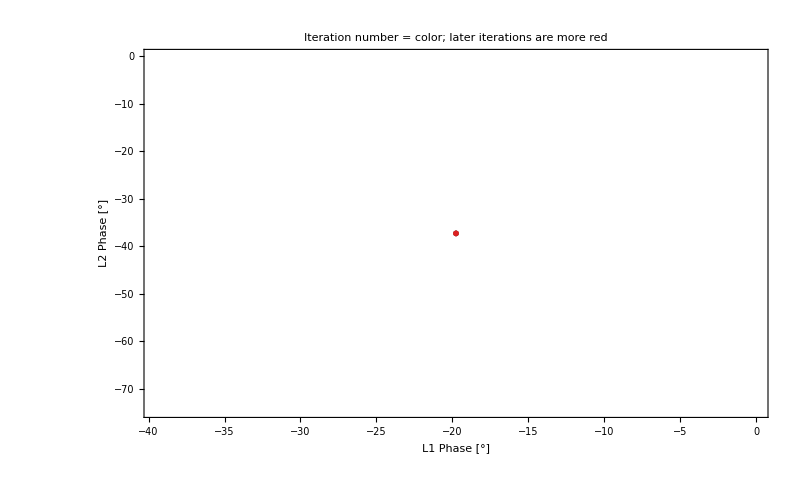

```mathematica
If[MemberQ[Keys[raw[[1]]],"L1PhaseSet"],
toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]
]
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

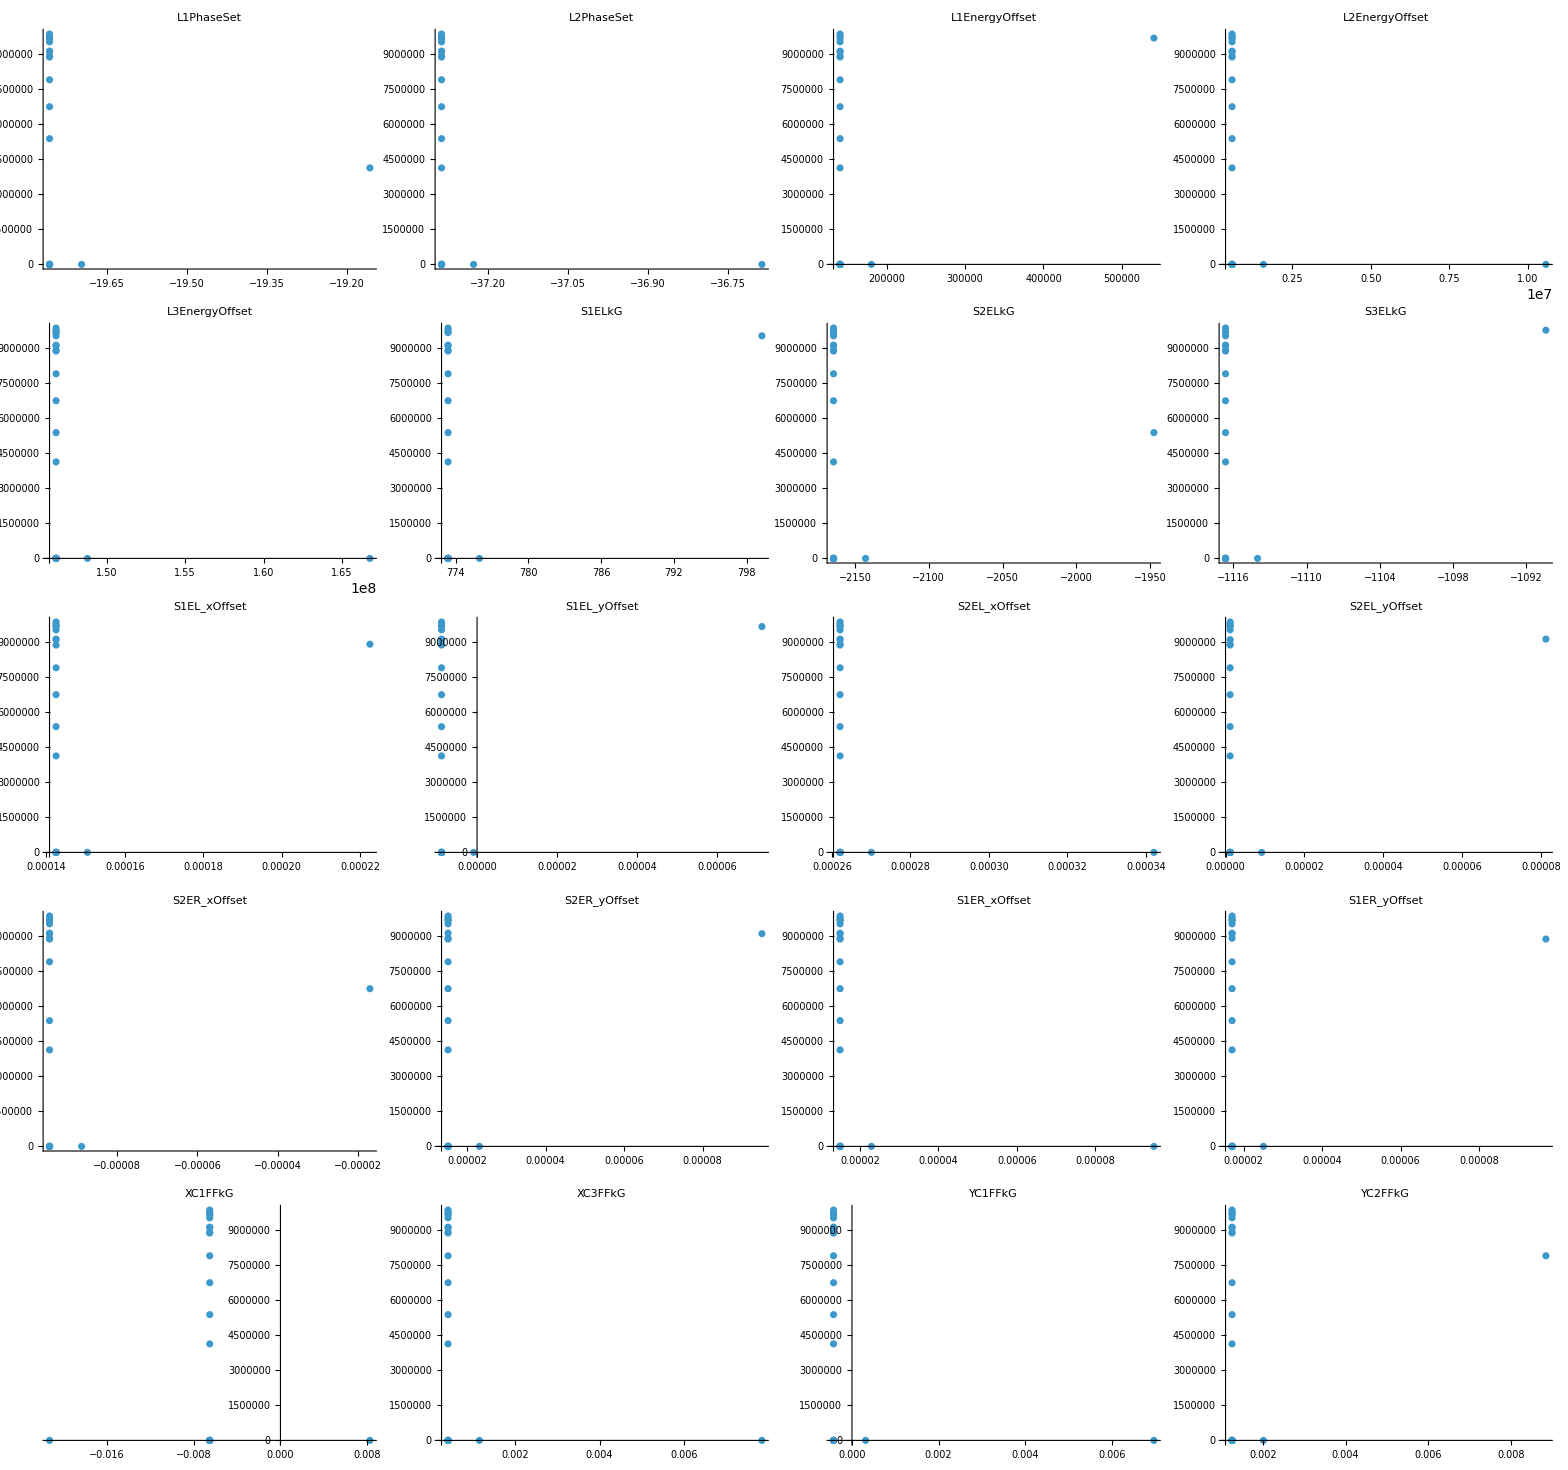

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

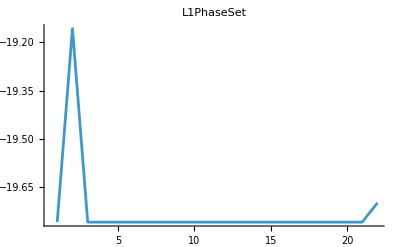
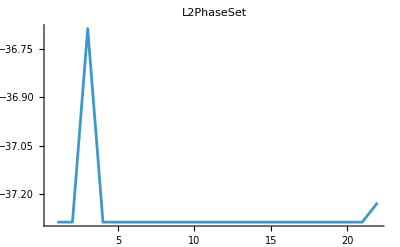
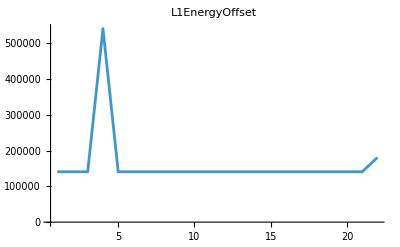
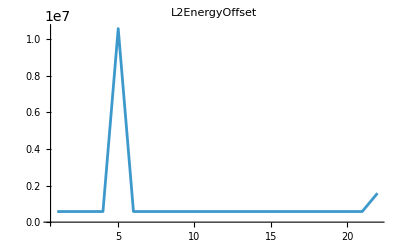
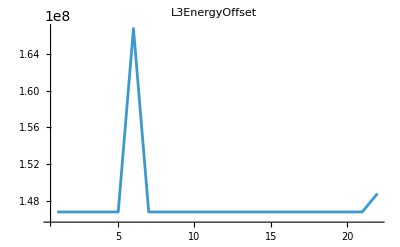
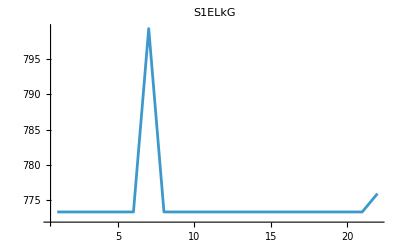
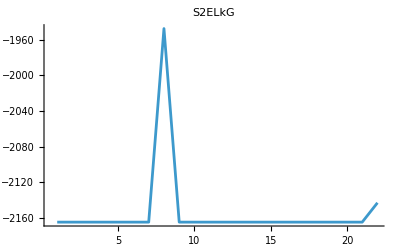
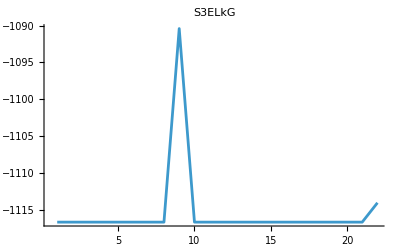
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Estimate maximizeMe asymptote

There’s no reason at all to think this is valid

```mathematica
(*runningBest = #["maximizeMe"]&/@raw;*)
```

```mathematica
Button["Calculate",

expr = a * Tanh[b ii]+c;
nlm=NonlinearModelFit[
Transpose[{Range[Length[runningBest]],runningBest}],
expr,
{
{a,Max[runningBest]},
{b,1/Length[runningBest]},
{c,Min[runningBest]}
},
ii,
Method->"NMinimize"
];

meanPredictionBands = nlm["MeanPredictionBands"];
singlePredictionBands = nlm["SinglePredictionBands"];
plotMe ={nlm["BestFit"]}~Join~meanPredictionBands~Join~singlePredictionBands;

img = Show[
ListPlot[
Transpose[{Range[Length[runningBest]],runningBest}],
PlotRange->{{0,Length[runningBest]*1.5},{0, Max[runningBest]*1.5}},
ImageSize->800
],

Plot[
plotMe,
{ii,0,Length[runningBest]*1.5},
PlotStyle->{{Opacity[0.5],Black},{Opacity[0.5],Red},{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Green}},
PlotRange->All
]

];

Print[
"Estimated limits: ",
Sort[
Limit[#,ii->Infinity]&/@plotMe
]
];
Print[img];
]
```

Calculate

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
(*Export[
"~/srData.csv",
Dataset[raw]
]*)
```

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.1577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-36.6864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,799.262,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-1947.45,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1090.4,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000222492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,0.0000711238,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000342051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,0.0000811634,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000169425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000095112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000949544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000970405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,0.00826539,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.00782914,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,0.00697419,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00885087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.6977,-37.2264,775.952,0.000150492,-8.762×10^-7,0.0000229544,0.0000250405,-2142.8,0.000270051,9.1634×10^-6,-0.0000889425,0.000023112,-1114.03,-0.0213346,0.00116914,0.000314186,0.00201087,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.1577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-36.6864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,799.262,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-1947.45,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1090.4,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000222492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,0.0000711238,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000342051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,0.0000811634,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000169425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000095112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000949544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000970405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,0.00826539,0.000429135,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.00782914,-0.000425814,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,0.00697419,0.00125087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.7577,-37.2864,773.362,0.000142492,-8.8762×10^-6,0.0000149544,0.0000170405,-2164.51,0.000262051,1.1634×10^-6,-0.0000969425,0.000015112,-1116.65,-0.00653461,0.000429135,-0.000425814,0.00885087,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.6977,-37.2264,775.952,0.000150492,-8.762×10^-7,0.0000229544,0.0000250405,-2142.8,0.000270051,9.1634×10^-6,-0.0000889425,0.000023112,-1114.03,-0.0213346,0.00116914,0.000314186,0.00201087,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -19.7577 | 0.554348
L2PhaseSet | -38.6737 | -37.2864 | 1.38732
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.000142492 | -0.000242763
S1EL_yOffset | -0.000241114 | -8.8762×10^-6 | 0.000232238
S2EL_xOffset | -0.00141787 | 0.000262051 | 0.00167992
S2EL_yOffset | 0.0000111705 | 1.1634×10^-6 | -0.0000100071
S2ER_xOffset | -0.00223816 | -0.0000969425 | 0.00214122
S2ER_yOffset | -0.000675996 | 0.000015112 | 0.000691108
S1ER_xOffset | 0.00100714 | 0.0000149544 | -0.000992182
S1ER_yOffset | 0.000398456 | 0.0000170405 | -0.000381415
XC1FFkG | 0.206455 | -0.00653461 | -0.21299
XC3FFkG | -0.0899164 | 0.000429135 | 0.0903455
YC1FFkG | -0.0022312 | -0.000425814 | 0.00180538
YC2FFkG | -0.00851158 | 0.00125087 | 0.00976246